# Minimal SMC model

## Setup

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]
<<"~thomasbuhrmann/Code/Mathematica/Dynamica/Dynamica.m";
```

Dynamica (Version 1.0.5 - 12/6/11), Copyright(c) 1993-2011 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## System Definition

Define and plot various environments / sensor transfer functions.

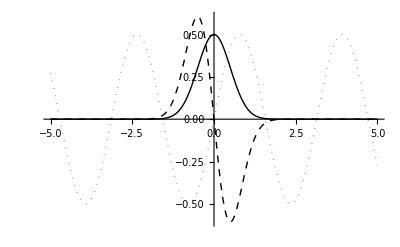

```mathematica
Gaus[x_,h_,w_]:=h Exp[-x^2/(2 w^2)];
GausDx[x_,h_,w_]:=-h/w^2 x Exp[-x^2/(2 w^2)];

height=0.5;
width=0.5;
Lin[x_]:=-2 x;
Sg[x_]:=Gaus[x,height,width];
Sgdx[x_]:=GausDx[x,height,width];
Ssin[x_]:=height*Sin[1/width*x];
M[s_]:=1 s;

(* Selection of environment *)
S[x_]:=Lin[x];

(* Setup dynamical system (Using Beer's Dynamica) *)
xLim=5;
sys=DynamicalSystem[{M[S[p]]},{{p,-xLim,xLim}},{}];

(* Plot sensor transfer functions *)
gPl=Plot[Gaus[x,height,width],{x,-xLim,xLim},PlotStyle->Black,PlotRange->{Automatic,{-0.65,0.65}}];
gdxPl=Plot[GausDx[x,height,width],{x,-xLim,xLim},PlotStyle->{Black,Dashed},PlotRange->{Automatic,{-0.65,0.65}}];
sinPl=Plot[Ssin[x],{x,-xLim,xLim},PlotStyle->{Gray,Dotted}];

Show[gPl,gdxPl,sinPl,PlotRange->All]
```

## Behaviour

### Phase portraits

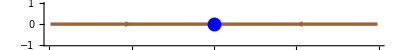

```mathematica
Show[DisplayFlow[sys,10.0],DisplayPhasePortrait[sys]]
```

### Trajectories

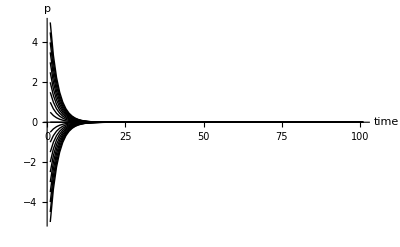

```mathematica
(* Create trajectories of position and sensor values *)
t0=Range[-xLim,xLim,0.5]; (* Initial conditions *)
DisplayTrajectories[sys,Partition[t0,1],20.0];
trjs=Table[Flatten[$Trajectories[[i]]],{i,1,Length[$Trajectories]}];
sTrjs=S[trjs];
len=Length[trjs[[1]]];

(* Show all created trajectories over time *)
allTrjPlots=Table[ListLinePlot[trjs[[i]],PlotStyle->Black,PlotRange->All],{i,1,Length[trjs]}];
Show[allTrjPlots,AxesLabel->{"time","p"}]
```

### SMCs ?

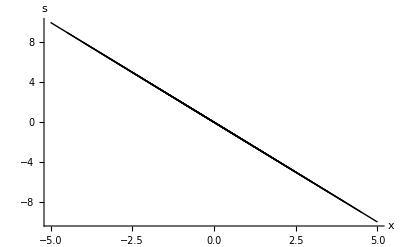

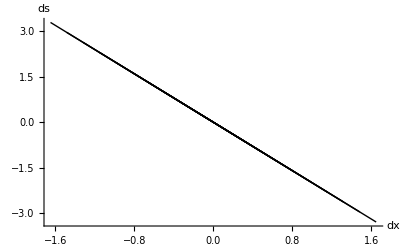

```mathematica
(* Sensor vs motor *)
allSvsM=Table[Graphics[Line[Transpose[{trjs[[i]],sTrjs[[i]]}],VertexColors->0.8-Range[0,0.8,1/len]]],{i,1,Length[trjs]}];
Show[allSvsM,Axes->True,AxesLabel->{"x","s"},AspectRatio->1/GoldenRatio]

(* Sensor d/dt vs motor d/dt *)
allSvsMDt=Table[Graphics[Line[Transpose[{Differences[trjs[[i]]],Differences[sTrjs[[i]]]}],VertexColors->0.8-Range[0,0.8,1/len]]],{i,1,Length[trjs]}];
Show[allSvsMDt,Axes->True,AxesLabel->{"dx","ds"},AspectRatio->1/GoldenRatio]
```